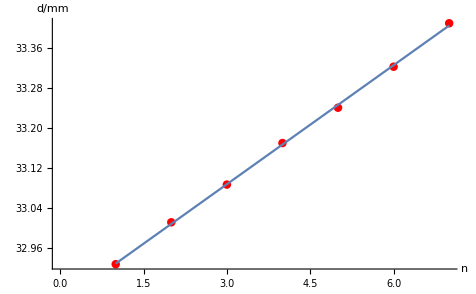
实验报告
系别：物理  班号：9组9号  姓名：盛凯枫  学号：1500011404  实验日期：2017年4月7日
实验名称：光源的时间相干性

一、数据处理
1. 测定几种光源的相干长度，并求出相干时间
白光：k1=2, λ1=5.50*10^2nm, ΔLmax1=k1*λ1=1.1μm, 相干时间Δt1 = ΔLmax1/c=3.7*10^-15s
白光经橙色玻璃滤光后：k2=10, λ2=6.25*10^2nm, ΔLmax2=k2*λ2=6.3μm, 相干时间Δt2 = ΔLmax2/c=2.1*10^-14s
白光经黄色滤光片滤光后：k3=33, λ3=5.78*10^2nm, ΔLmax3=k3*λ3=19μm, 相干时间Δt3 = ΔLmax3/c=6.3*10^-14s
汞黄光：d0=32.89210mm, dmax=41.14620mm, ΔLmax4=2(dmax-d0)=16.5mm, 相干时间Δt4 = ΔLmax4/c=5.5*10^-11s

2. 两种方法测定汞双黄线的波长差
(1)、拍的节点位置记录表
拍的节点 | 1 | 2 | 3 | 4 | 5 | 6 | 7
d/mm | 32.92822 | 33.0119 | 33.08725 | 33.17022 | 33.24082 | 33.32271 | 33.4095
-Graphics-
拟合直线方程 y = 32.8502+0.0792532 x，Δd=0.0793mm±0.0008mm, λ=578nm, Δλ=λ^2/(2Δd)=2.11±0.02nm
(2)、两相邻可见度为零的区间内干涉条纹数Δk=272, Δλ=λ/Δk=2.13nm, 与方法1测量结果之差在误差范围内

二、分析与讨论
本实验在测量干涉条纹数时，对是否存在干涉条纹的判断过于主观，特别是在白光经滤光片滤光以及汞黄光的观察时，条纹清晰度与光源亮度、外界杂散光强度、观察角度等都有较大关系，如果能用光电记录仪记录光强再做分析可以使实验科学很多。

```mathematica
data={32.92822,33.01190,33.08725,33.17022,33.24082,33.32271,33.40950}
```

{32.9282,33.0119,33.0873,33.1702,33.2408,33.3227,33.4095}

```mathematica
TextGrid[{Table[i,{i,1,7}]//Prepend["拍的节点"],SetPrecision[data,7]//Prepend["d/mm"]},Frame->All,ItemSize->Full,Alignment->{Center,Center}]
```

拍的节点 | 1 | 2 | 3 | 4 | 5 | 6 | 7
d/mm | 32.92822 | 33.0119 | 33.08725 | 33.17022 | 33.24082 | 33.32271 | 33.4095

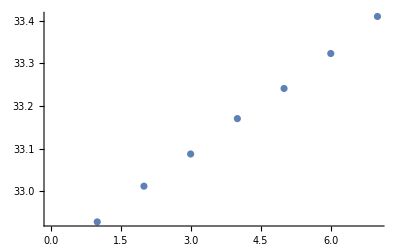

```mathematica
ListPlot[data]
```

```mathematica
LinearModelFit[Table[{i,data[[i]]},{i,1,7}],x,x]
```

FittedModel[32.8502+0.0792532 x]

```mathematica
%3["AdjustedRSquared"]
```

```mathematica
√0.9994356685580666
```

```mathematica
√(1/0.99944^2-1)/5
```

0.0149729

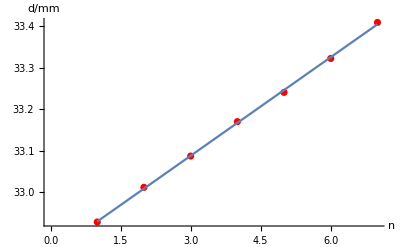

```mathematica
Show[ListPlot[Table[{i,data⟦i⟧},{i,1,7}],PlotStyle->Red],Plot[%3[x],{x,1,7}],AxesLabel->{"n","d/mm"}]
```

```mathematica
Table[data[[i+1]]-data[[i]],{i,1,6}]
```

```mathematica
ave[{0.08367999999999398,0.07535000000000025,0.0829700000000031,0.07059999999999889,0.08189000000000135,0.08679000000000059}]
```

0.0802133

```mathematica
stdvar[{0.08367999999999398,0.07535000000000025,0.0829700000000031,0.07059999999999889,0.08189000000000135,0.08679000000000059}]
```

```mathematica
0.005503770424798802/0.08
```

0.0687971

```mathematica
578^2/(2*79.3*10^3)
```

2.10646